# Economics 381

## Homework

## Problem Set 1

### 1: Hands Dirty with Data

#### a.) Downloading the Data

```mathematica
SetDirectory["/Users/spencerlyon2/Documents/School/Semesters/Winter 2012/Economics 381/Homeworks/Data"];
CPILFESL =priceIndex= Import["CPILFESL.csv"];

PAYEMS =payrollEmployment= Import["PAYEMS.csv"];
GDPC96 = gdp = Import["GDPC96.csv"];
Dimensions[#]&/@{payrollEmployment,gdp,priceIndex};
```

#### b.) Plot GDP and PayrollEmp on same axis from Q1-1948 to Q3-2011

```mathematica
{payrollDate,payrollData} = Transpose[payrollEmployment[[38;;292]]];
{gdpDate,gdpData} = Transpose[gdp[[5;;259]]];
Dimensions[#]&/@{payrollData,gdpData}
```

(255
255)

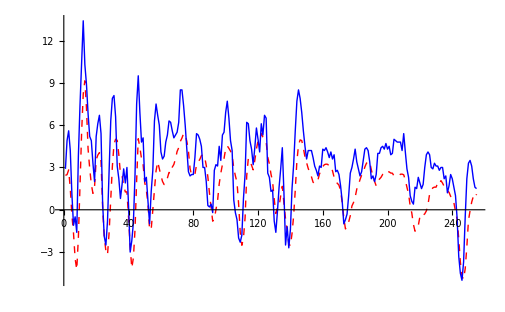

0.812196

```mathematica
ListPlot[{payrollData,gdpData},Joined->True,PlotStyle->{{Red,Dashed},{Blue,Thick}}]
Correlation[payrollData,gdpData]
```

I believe these two series are so closely related (positively) because the higher the GDP, the more goods the US produces. The more goods the US produces, the more workers it will need and the higher the employment level will be.

#### c.) Plot GDP and the CPI from Q!-1958 to Q3-2011

```mathematica
{priceDates,priceData }= Transpose[priceIndex[[6;;220]]];
newGdpData = gdpData[[40;;254]];
Dimensions[#]&/@{priceData,newGdpData}
```

(215
215)

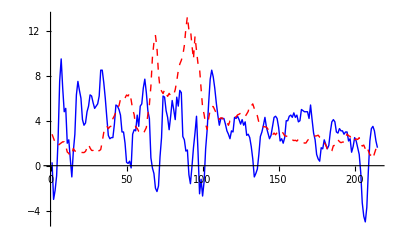

-0.198922

```mathematica
ListPlot[{newGdpData,priceData},Joined->True,GridLines->{{},{}},PlotStyle->{{Blue,Thick},{Red,Dashed}}]
Correlation[newGdpData,priceData]
```

I believe there is a somewhat weak negative relationship between GDP and the CPI because in times when GDP is high, consumption in future periods will be higher. This is due to higher average income for a US citizen in previous periods. This effect doesn’t completely take place in the same period, so a lagged effect of GPD on the CPI could explain why the relationship is weak. 

The sign of the correlation can also be explained by the same lagged idea that was spoken of before. As GDP is increasing, CPI will follow and increase in later periods. When GPD stops increasing as much ( negative second derivative) the CPI is still rising because of increased income in previous periods. This results in the direction of change in the two statistics to be in the opposite direction much of the time.

Both of these ideas can be seen clearly in the graph above.

### 2.) Problems and Applications: Chapter 2, #6: S A farmer grows a bushel of wheat and sells it to a miller for $1.00. The Miller turns the wheat into flour and then sell the flour to a Baker for $3.00. The baker uses the flour to make bread and sells the bread to an engineer for $6.00. The engineer eats the bread. What is the value added by each person? What is GDP?

### 3.) Chapter 2, Related employment Question: Suppose an economy is made up of 100 people who are in the following mutually exclusive categories shown in Table 1. Three concepts are at play here: adult population, workforce, and labor force. A simple definition of the workforce is everybody in the economy who is 16 or older. So the labor force is a subset of the workforce, and the workforce is a subset of the adult population.

#### (a) What is the percent of the adult population not in the labor force?

#### (b) What is the labor force participation rate?

#### (c) What is the unemployment rate?